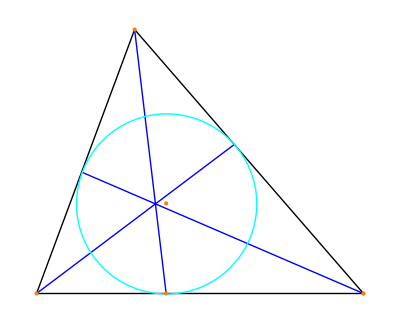

```mathematica
K={-5.,0.};L={-0.5,7*√3}; M={10.,0.};
poluperimetr[A1_,A2_,A3_]:=0.5*(Norm[A1-A2]+Norm[A1-A3]+Norm[A2-A3])

radiusVpis[A1_,A2_,A3_]:=((poluperimetr[A1,A2,A3]-Norm[A1-A2])*(poluperimetr[A1,A2,A3]-Norm[A1-A3])*(poluperimetr[A1,A2,A3]-Norm[A2-A3])/poluperimetr[A1,A2,A3])^0.5;
kosinusAlpha[A1_,A2_,A3_]:=((Norm[A1-A3])^2+(Norm[A1-A2])^2-(Norm[A2-A3])^2)/(2*(Norm[A1-A3])*(Norm[A1-A2]));
kosinusAlphaPopolam[A1_,A2_,A3_]:=√((1+kosinusAlpha[A1,A2,A3])/2);
sinusAlphaPopolam[A1_,A2_,A3_]:=√(1-(kosinusAlphaPopolam[A1,A2,A3])^2);
tochkaKasania1[A1_,A2_,A3_]:=A1+((A3-A1)*radiusVpis[A1,A2,A3]*kosinusAlphaPopolam[A1,A2,A3])/((Norm[A3-A1])*sinusAlphaPopolam[A1,A2,A3]);

centrvpis[A1_,A2_,A3_]:=tochkaKasania1[A1,A2,A3] +({-(A3-A1).{0,1},(A3-A1).{1,0}}/Norm[A3-A1])*radiusVpis[A1,A2,A3];
tochkaKasania2[A1_,A2_,A3_]:=centrvpis[A1,A2,A3]+radiusVpis[A1,A2,A3]*({-(A2-A1).{0,1},(A2-A1).{1,0}}/Norm[A2-A1]);
tochkaKasania3[A1_,A2_,A3_]:=centrvpis[A1,A2,A3]+radiusVpis[A1,A2,A3]*({(A2-A3).{0,1},-(A2-A3).{1,0}}/Norm[A2-A3]);



v={K,L,M}~Join~{tochkaKasania1[K,L,M],centrvpis[K,L,M],tochkaKasania2[K,L,M],tochkaKasania3[K,L,M]};
rvpis=radiusVpis[K,L,M];
Graphics[GraphicsComplex[v,{Thin,Line[{1,2,3,1}],Blue,Thick,Line[{2,4}],Line[{3,6}],Line[{1,7}],Cyan,Circle[5,rvpis],Orange,PointSize[Large],Point[{1,2,3,4,5}]}]]
```